## Important definitions.

```mathematica
Sx[ϕ_]:={{0,Exp[ⅈ ϕ],0},{Exp[-ⅈ ϕ],0,0},{0,0,0}};
Sy[ϕ_]:={{0,0,Exp[-ⅈ ϕ]},{0,0,0},{Exp[ⅈ ϕ],0,0}};
Sz[ϕ_]:={{0,0,0},{0,0,Exp[ⅈ ϕ]},{0,Exp[-ⅈ ϕ],0}};
H[ϕ_,px_,py_,pz_]:=px Sx[ϕ] + py Sy[ϕ] + pz Sz[ϕ];
MatrixForm[Sx[π/2]]
MatrixForm[Sy[π/2]]
MatrixForm[Sz[π/2]]
MatrixForm[H[π/2,p1,p2,p3]]
```

(0 | ⅈ | 0
-ⅈ | 0 | 0
0 | 0 | 0)

(0 | 0 | -ⅈ
0 | 0 | 0
ⅈ | 0 | 0)

(0 | 0 | 0
0 | 0 | ⅈ
0 | -ⅈ | 0)

(0 | ⅈ p1 | -ⅈ p2
-ⅈ p1 | 0 | ⅈ p3
ⅈ p2 | -ⅈ p3 | 0)

```mathematica
PropagatorS[ω_,p1_,p2_,p3_]:=Inverse[-ⅈ ω IdentityMatrix[3] + H[π/2,v p1,v p2,v p3]];
MatrixForm[Simplify[PropagatorS[ω,p1,p2,p3]]]
```

((ⅈ (p3^2 v^2+ω^2))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2)) | (ⅈ v (p2 p3 v+p1 ω))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2)) | (ⅈ v (p1 p3 v-p2 ω))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2))
(ⅈ v (p2 p3 v-p1 ω))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2)) | (ⅈ (p2^2 v^2+ω^2))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2)) | (ⅈ v (p1 p2 v+p3 ω))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2))
(ⅈ v (p1 p3 v+p2 ω))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2)) | (ⅈ v (p1 p2 v-p3 ω))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2)) | (ⅈ (p1^2 v^2+ω^2))/(ω (p1^2 v^2+p2^2 v^2+p3^2 v^2+ω^2)))

## Electron Self-Energy.

```mathematica
Simplify[D[1/((k1-p1)^2+k2^2+k3^2),p1]/.p1->0]
```

(2 k1)/((k1^2+k2^2+k3^2)^2)

```mathematica
Integrate[1/(ω^2+v^2 k^2),{ω,-Infinity,Infinity},Assumptions->{v,k}∈Reals]
```

π/Abs[k v]

```mathematica
Integrate[Sin[θ] Cos[θ] Cos[θ],{θ,0,π}]
```

2/3

## Particle-Hole Polarization of the photon.

```mathematica
Simplify[Tr[PropagatorS[ω,k1,k2,k3].PropagatorS[ω,k1,k2,k3]]]
```

-(k1^4 v^4+k2^4 v^4+2 k2^2 k3^2 v^4+k3^4 v^4+2 k1^2 (k2^2+k3^2) v^4+3 ω^4)/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2)

```mathematica
Integrate[1/((ω+ⅈ δ)^2(ω^2+v^2 p^2)^2),{ω,-Infinity,Infinity},Assumptions->{{v,p}∈Reals&&δ>0}]
```

ConditionalExpression[-(π (3 p v+δ))/(2 p^3 v^3 (p v+δ)^3),p v>0]

```mathematica
Integrate[ω^2/((ω^2+v^2 p^2)^2),{ω,-Infinity,Infinity},Assumptions->{v,p}∈Reals]
```

π/(2 p v)

```mathematica
PolarizationPI[Ω_,q1_,q2_,q3_]:=Simplify[Tr[PropagatorS[Ω+ω,q1+k1,q2+k2,q3+k3].PropagatorS[ω,k1,k2,k3]]]
```

```mathematica
Simplify[D[PolarizationPI[0,q1,0,0],{q1,2}]/.q1->0]
```

1/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^4)2 (k2^6 v^8+3 k2^4 k3^2 v^8+k3^6 v^8+k3^2 v^4 ω^4+2 v^2 ω^6+k1^4 (k2^2 v^8+k3^2 v^8+2 v^6 ω^2)+k2^2 v^4 (3 k3^4 v^4+ω^4)+2 k1^2 (k2^4 v^8+k3^4 v^8+k3^2 v^6 ω^2-6 v^4 ω^4+k2^2 v^6 (2 k3^2 v^2+ω^2)))

```mathematica
Simplify[2 (k2^6 v^8+3 k2^4 k3^2 v^8+k3^6 v^8+k1^4 (k2^2 v^8+k3^2 v^8)+k2^2 v^4 (3 k3^4 v^4)+2 k1^2 (k2^4 v^8+k3^4 v^8+k2^2 v^6 (2 k3^2 v^2)))]
```

2 (k2^2+k3^2) (k1^2+k2^2+k3^2)^2 v^8

```mathematica
Collect[2(k3^2 v^4 ω^4+2 v^2 ω^6+2 k1^4 v^6 ω^2+k2^2 v^4 ω^4+2 k1^2(k3^2 v^6 ω^2-6 v^4 ω^4+k2^2 v^6 ω^2)),ω]
```

2 (2 k1^4 v^6+2 k1^2 k2^2 v^6+2 k1^2 k3^2 v^6) ω^2+2 (-12 k1^2 v^4+k2^2 v^4+k3^2 v^4) ω^4+4 v^2 ω^6

```mathematica
Integrate[1/((ω+ⅈ δ)^2(ω^2+v^2 k^2)^4),{ω,-Infinity,Infinity},Assumptions->{{v,k}∈Reals&&δ>0}]
```

ConditionalExpression[-(π (35 k^3 v^3+47 k^2 v^2 δ+25 k v δ^2+5 δ^3))/(16 k^7 v^7 (k v+δ)^5),k v>0]

```mathematica
Integrate[1/((ω^2+v^2 k^2)^4),{ω,-Infinity,Infinity},Assumptions->{v,k}∈Reals]
```

(5 π Abs[k] Abs[v])/(16 k^8 v^8)

```mathematica
Integrate[ω^2/((ω^2+v^2 k^2)^4),{ω,-Infinity,Infinity},Assumptions->{v,k}∈ Reals]
```

π/(16 k^5 v^5)

```mathematica
Integrate[ω^4/((ω^2+v^2 k^2)^4),{ω,-Infinity,Infinity},Assumptions->{v,k}∈Reals]
```

π/(16 k^3 v^3)

```mathematica
Integrate[Sin[θ](-2/(k v)+27/(16k v)Cos[θ] Cos[θ]),{θ,0,π},Assumptions->{k,v}∈Reals]
```

-23/(8 k v)

```mathematica
23/(8* 4 π^2*2)
```

23/(64 π^2)

## RG equation and RG Flow.

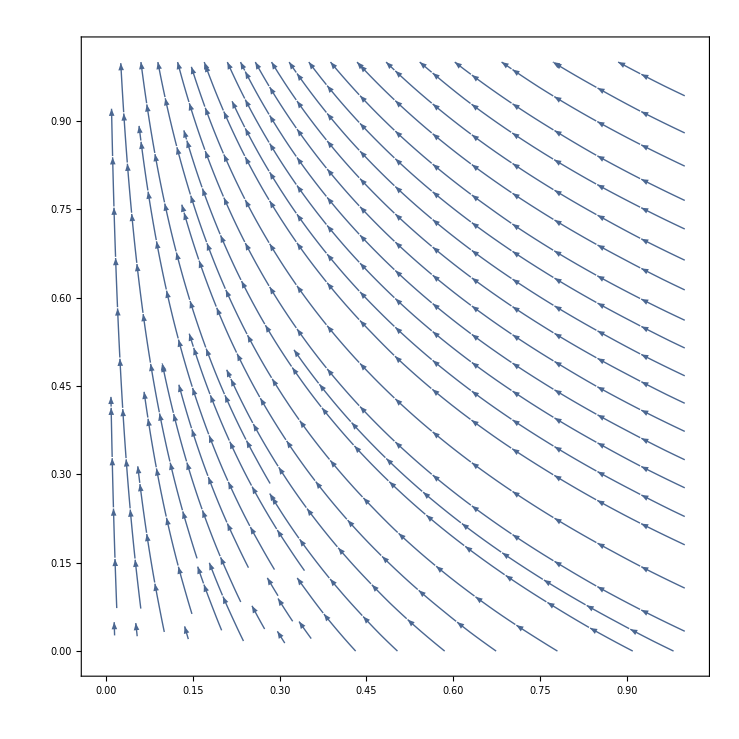

```mathematica
StreamPlot[{(-23 g^3)/(64 π^2),g^2/(6 π^2)},{g,0,1},{v,0,1}]
```

## ϕ ≠ π/2case [no SO(3) symmetry].

```mathematica
MatrixForm[δϕ IdentityMatrix[3]. Simplify[SeriesCoefficient[H[δϕ+π/2,v p1,v p2,v p3],{δϕ,0,1}]]]
```

(0 | -p1 v δϕ | -p2 v δϕ
-p1 v δϕ | 0 | -p3 v δϕ
-p2 v δϕ | -p3 v δϕ | 0)

```mathematica
ΔPropagatorS[ω_,p1_,p2_,p3_]:=Simplify[SeriesCoefficient[Inverse[-ⅈ ω IdentityMatrix[3]+ v H[δϕ+π/2,p1,p2,p3]],{δϕ,0,1}]];
MatrixForm[ΔPropagatorS[ω,k1,k2,k3]]
```

(-(6 k1 k2 k3 v^3 (k3^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2) | (-6 k1 k2 k3 v^4 (k2 k3 v+k1 ω)+v ω (2 k2 k3 v-k1 ω) (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2) | (6 k1 k2 k3 v^4 (-k1 k3 v+k2 ω)-v ω (2 k1 k3 v+k2 ω) (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2)
(6 k1 k2 k3 v^4 (-k2 k3 v+k1 ω)-v ω (2 k2 k3 v+k1 ω) (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2) | -(6 k1 k2 k3 v^3 (k2^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2) | (-6 k1 k2 k3 v^4 (k1 k2 v+k3 ω)+v ω (2 k1 k2 v-k3 ω) (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2)
(-6 k1 k2 k3 v^4 (k1 k3 v+k2 ω)+v ω (2 k1 k3 v-k2 ω) (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2) | (6 k1 k2 k3 v^4 (-k1 k2 v+k3 ω)-v ω (2 k1 k2 v+k3 ω) (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2) | -(6 k1 k2 k3 v^3 (k1^2 v^2+ω^2))/(ω^2 (k1^2 v^2+k2^2 v^2+k3^2 v^2+ω^2)^2))

```mathematica
Integrate[1/((ω+ⅈ δ)^2(ω^2+v^2 k^2)^2),{ω,-Infinity,Infinity},Assumptions->{{v,k}∈Reals&&δ>0}]/.δ->0
```

ConditionalExpression[-(3 π)/(2 k^5 v^5),k v>0]

```mathematica
Integrate[1/(ω^2+v^2 k^2),{ω,-Infinity,Infinity},Assumptions->{v,k}∈Reals]
```

π/Abs[k v]

```mathematica
Integrate[(Sin[θ])^5(Cos[θ])^2,{θ,0,π}]*Integrate[(Cos[ϕ])^2(Sin[ϕ])^2,{ϕ,0,2π}]
```

(4 π)/105

```mathematica
Integrate[(Sin[θ])^3,{θ,0,π}]*Integrate[(Cos[ϕ])^2,{ϕ,0,2π}]
```

(4 π)/3

```mathematica
((36π)/105-(4π)/3)* 1/(8 π^3)
```

-13/(105 π^2)

```mathematica
13/105-1/6
```

-3/70

## RG of three parametres: δϕ, v and g.

Calculation of one-loop diagrams can give beta functions of the parameters:

ⅆv/(ⅆ log b)=g^2/(6 π^2)
ⅆg/(ⅆ log b)= -(23 g^3)/(64 π^2 v)
(ⅆ δϕ)/(ⅆ log b)=-(3δϕ)/(70 π^2)(g^2/v)
⟹(ⅆ (g^2/v))/(ⅆ log b) =-85/(96 π^2)(g^2/v)^2

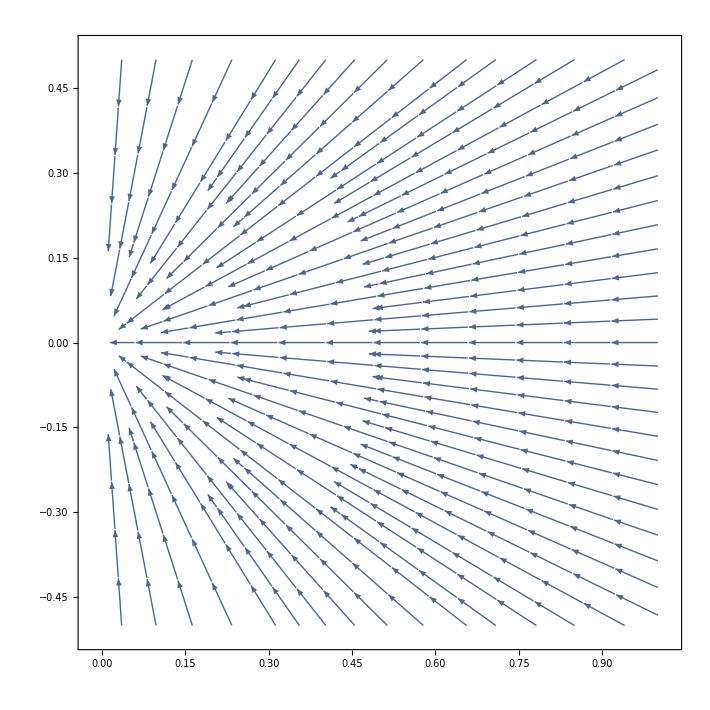

```mathematica
StreamPlot[{-x^2,-x y},{x,0,1},{y,-1/2,1/2}]
```